```mathematica
parasiteload={0,1,2,3,4,5,6,7,8,9,10};
plotchat[P_]:={transmisstion=Prepend[ConstantArray[P,10],1-P];
X={transmisstion⟦1⟧ 100};
exact=Last[Table[AppendTo[X,Last[X] transmisstion⟦i⟧],{i,2,10}]];
AppendTo[exact,100-Total[exact]],
BarChart[exact,PlotRange->{Automatic,{0,100}},ChartStyle->Table[RGBColor[1,1-i,1-i],{i,0,1,0.1}]]}
```

```mathematica
plots=Table[plotchat[P],{P,{0.01,0.05,0.1,0.3,0.5,0.7,0.9,0.95,0.99}}];
```

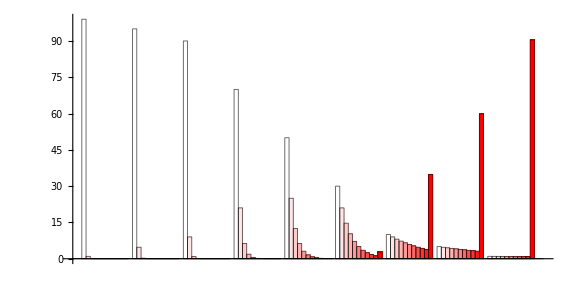

```mathematica
BarChart[plots⟦All,1⟧,ChartStyle->{EdgeForm[{Opacity[0.7,Black],Thickness[.001]}],Table[RGBColor[1,1-i,1-i],{i,0,1,0.1}]},AspectRatio->0.5,ImageSize->Large,AxesStyle->{Thickness[0.001],Directive[Thick,Black,14]},BarSpacing->{0,1}]
```

```mathematica
Pvalues={0.01,0.05,0.1,0.3,0.5,0.7,0.9,0.95,0.99};
means=Table[(plots⟦All,1⟧⟦i,#⟧)/100 parasiteload⟦#⟧&/@Range[1,11],{i,1,Length[plots⟦All,1⟧]}];
totalmean=Total[#]&/@means;
squaredmeans=Table[(plots⟦All,1⟧⟦i,#⟧)/100 parasiteload⟦#⟧^2&/@Range[1,11],{i,1,Length[plots⟦All,1⟧]}];
variances=Table[Total[squaredmeans⟦i⟧]-totalmean⟦i⟧^2,{i,1,Length[plots⟦All,1⟧]}];
xymeans=Partition[Riffle[Pvalues,totalmean],2];
xyvariances=Partition[Riffle[Pvalues,variances],2];
```

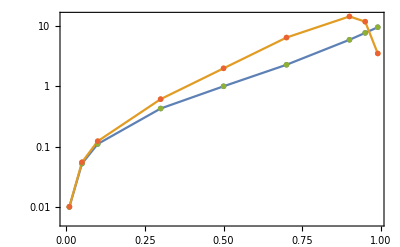

```mathematica
ListLogPlot[{xymeans,xyvariances,xymeans,xyvariances},Joined->{True,True,False,False},Frame->True,PlotMarkers->{-Graphics-,-Graphics-},FrameStyle->Directive[Black,Thickness[0.003]]]
```